```mathematica
Quit[];
Clear["Global`*"]
```

```mathematica
Import["/Users/conordyson/Documents/GitHub/BHPT/KerrGeodesics/KerrGeodesicsTest/Kernel/KerrGeoPlunge.m"];
```

```mathematica
a =0.1;
M=1;
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
orbit = KerrGeoPlunge[a, "ISSOIncParam", π/3];
{RI,R4} = orbit["RadialRoots"][[3;;]];
{Z1,Z2}=orbit["PolarRoots"];
{t,r,θ,ϕ} = orbit["Trajectory"];
{KR,KZ} = orbit["EllipticBasis"];
z[λ_] = Cos[θ[λ]];
{ϵ,L,Q} = orbit["ConstantsOfMotion"];
```

## Plots and Tests

### 3D Plots

```mathematica
P1 = ParametricPlot3D[{Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]},{λ,5,60}, PlotStyle->Red,PlotRange->All];
P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},MaxRecursion->4,PlotStyle->{Opacity[1],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
Show[P1,P2]
```

-Graphics3D-

### Azimuthal Plots

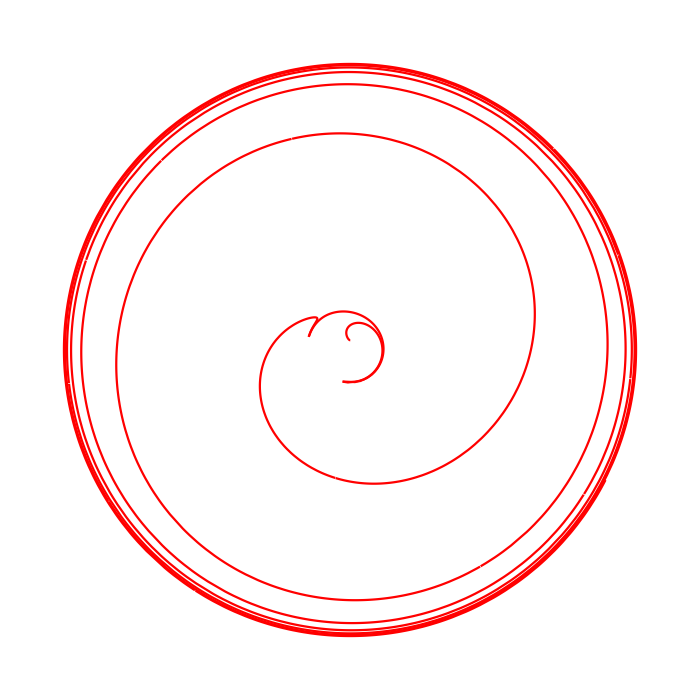

```mathematica
ParametricPlot[{Re[r[λ] ]Cos[Re[ϕ[λ]]],Re[r[λ]]  Sin[Re[ϕ[λ]]]},{λ,0,10},ImageSize->700,MaxRecursion->10,Axes->False,PlotStyle->Red,PlotRange->All]
```

### Testing Solutions

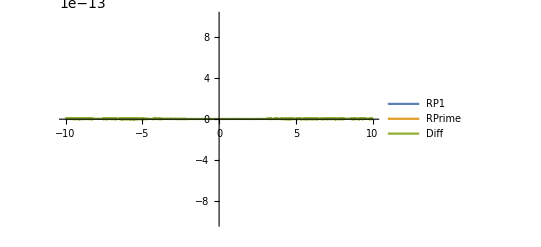

```mathematica
RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)

Plot[{RPoly1[r[λ]], (r'[λ])^2, (r'[λ])^2- RPoly1[r[λ]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,Diff},  PlotRange->{{-10,10},{-0.0000000000010,0.0000000000010}}]
```

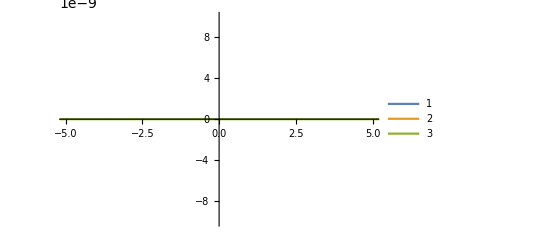

```mathematica
Polyθ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Plot[{(z'[λ])^2, Polyθ[λ], (z'[λ])^2- Polyθ[λ]}, {λ,-10,10}, PlotLegends->Automatic ,PlotLegends->{PolyθQ,θQ,θQ-PolyθQ}, PlotRange->{{-5,5},{-0.000000010,0.000000010}}]
```

```mathematica
|
```

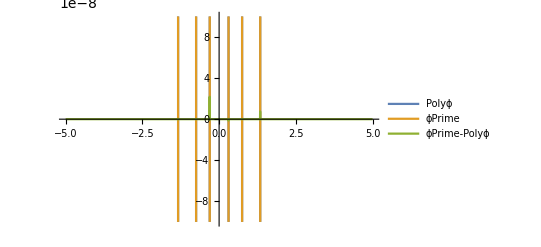

```mathematica
(*Plot[Im[ϕ[λ]],{λ,-5,5}]*)
Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) + L/(1-z[λ]^2)-a*ϵ
Plot[{Polyϕ[λ],Re[ϕ'[λ]],Re[ϕ'[λ]-Polyϕ[λ]]},{λ,-5,5}, PlotRange->{{-5,5},{-0.00000010,0.00000010}},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ}]
```

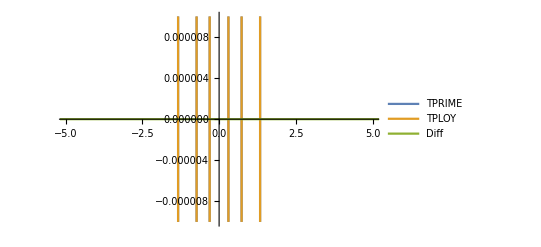

```mathematica
TPoly[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)-a^2 ϵ(1-z[λ]^2)+a*L
Plot[{Re[t'[λ]],TPoly[λ],Re[t'[λ]]-TPoly[λ] },{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff}, PlotRange->{{-5,5},{-0.000010,0.000010}}]
```

## Radial Flow

### Equations

```mathematica
Λ = z[(4 EllipticK[KZ])/Z2];
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);
RadialInFlowTrue[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ(1-(Z1 JacobiSN[ (2 Z2 √(r-R4))/(√((1-ϵ^2) (RI-r) (R4-RI)^2))+EllipticK[KZ],KZ])^2));

RadialInFlowPolarAvg[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ + ( Z2^2/(1-ϵ^2)(1-EllipticE[KZ]/EllipticK[KZ])  ));
RadialInFlowHalfAvg[r_]:= (-Sqrt[(ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ);
RadialInFlowEquitorial[r_]:= (-Sqrt[(1-ϵ^2)(RI-r)^3(r)])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ);
```

### Analysis and Plots

#### Plots of Flows

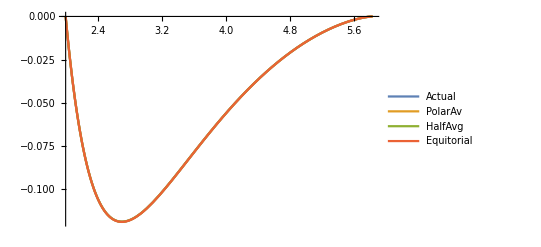

```mathematica
Plot[{RadialInFlowTrue[r],RadialInFlowPolarAvg[r],RadialInFlowHalfAvg[r],RadialInFlowEquitorial[r]},{r,RP,RI}, PlotRange->All,PlotLegends->{"Actual","PolarAv","HalfAvg","Equitorial"}]
```

#### Errors

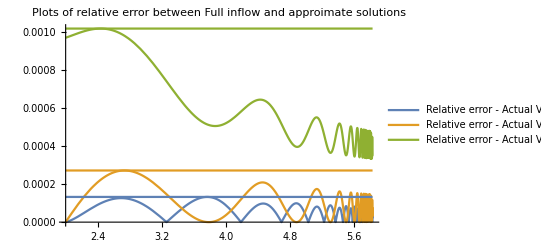

```mathematica
Q1 = Plot[{Abs[(RadialInFlowTrue[r] - RadialInFlowPolarAvg[r])/RadialInFlowTrue[r]] ,Abs[(RadialInFlowTrue[r] - RadialInFlowHalfAvg[r])/RadialInFlowTrue[r]],Abs[(RadialInFlowTrue[r] - RadialInFlowEquitorial[r])/RadialInFlowTrue[r]] },{r,RP,RI-0.001}, PlotRange->All, PlotLabel->"Plots of relative error between Full inflow and approimate solutions",PlotLegends->{"Relative error - Actual Vs PolarAv","Relative error - Actual Vs HalfAvg","Relative error - Actual Vs Equitorial"}];

Max1 = NMaximize[{Abs[(RadialInFlowTrue[x] - RadialInFlowPolarAvg[x])/RadialInFlowTrue[x]], RP+0.001<=x<=RI-0.001},x][[1]];
Max2 = NMaximize[{Abs[(RadialInFlowTrue[x] - RadialInFlowHalfAvg[x])/RadialInFlowTrue[x]], RP+0.001<=x<=RI-0.001},x][[1]];
Max3 = NMaximize[{Abs[(RadialInFlowTrue[x] - RadialInFlowEquitorial[x])/RadialInFlowTrue[x]], RP+0.001<=x<=RI-0.001},x][[1]];

Q2 =ParametricPlot[{ {r,Max1},{r,Max2},{r,Max3}},{r,RP,RI}];


Show[Q1,Q2]
```

### ContourPlotOverParamaterSpace

#### The matrices

```mathematica
<<KerrGeodesics`
n = 20;

a = Table[i, {i,0.01,0.99,0.999/n}];
 θINC =ArcCos[ Table[i, {i,0.01,0.99,0.999/n}]];

f[x_,y_]:= {x,y}

aMatrixFunc[x_] :=x[[1]];
 aMF=Map[aMatrixFunc,Outer[f,a,  θINC ],{2}];

θMatrixFunc[x_] :=x[[2]];
 θMF=Map[χMatrixFunc,Outer[f,a,  θINC  ],{2}];

ErrorPolarAvgFunction[x_]:={x[[1]],x[[2]],ErrorModuleFlowPolarAvg[x[[1]],x[[2]]]};
ErrorPolarAvgMF = Map[ErrorPolarAvgFunction,Outer[f,a,  θINC  ],{2}];

ErrorHalfAvgFunction[x_]:={x[[1]],x[[2]],ErrorModuleFlowHalfAvg[x[[1]],x[[2]]]};
ErrorHalfAvgMF = Map[ErrorHalfAvgFunction,Outer[f,a,  θINC  ],{2}];

ErrorEquatorFunction[x_]:={x[[1]],x[[2]],ErrorModuleFlowEquitorial[x[[1]],x[[2]]]};
ErrorEquatorMF = Map[ErrorEquatorFunction,Outer[f,a,  θINC  ],{2}];
```

```mathematica
ErrorModuleFlowPolarAvg[0.4,0.2]
```

0.000142357

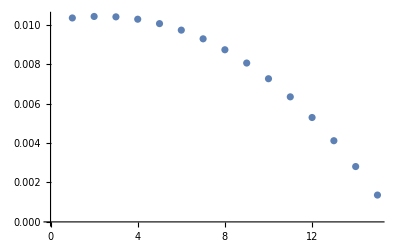

```mathematica
ListPlot[ErrorEquatorMF[[5,;;,3]]]
```

```mathematica
ListPlot3D[Flatten[ErrorEquatorMF,1],InterpolationOrder->5,ScalingFunctions->"Reverse",PlotLegends->Automatic,PlotRange->{0,0.5},ColorFunction->"DeepSeaColors"]
ListPlot3D[Flatten[ErrorHalfAvgMF,1],InterpolationOrder->5,ScalingFunctions->"Reverse",PlotLegends->Automatic,PlotRange->{0,0.5},ColorFunction->"DeepSeaColors"]
ListPlot3D[Flatten[ErrorPolarAvgMF,1],InterpolationOrder->5,ScalingFunctions->"Reverse",PlotLegends->Automatic,PlotRange->{0,0.5},ColorFunction->"DeepSeaColors"]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

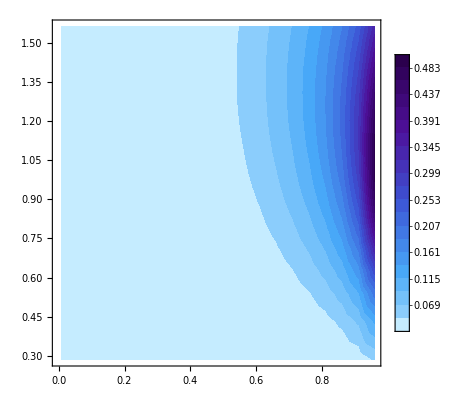

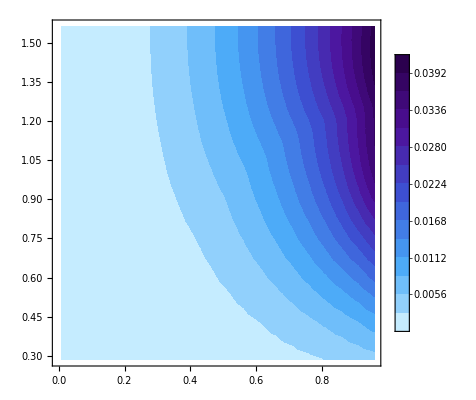

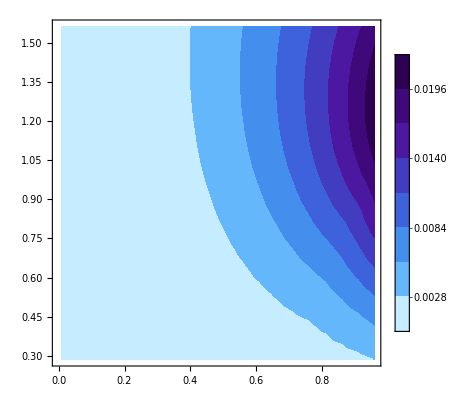

```mathematica
Q1 = ListContourPlot[Flatten[ErrorEquatorMF,1],InterpolationOrder->5,PlotLegends->Automatic,PlotRange->{0,0.5},ScalingFunctions->"Reverse",ColorFunction->"DeepSeaColors",Contours->20, ContourStyle->None]
Q2 = ListContourPlot[Flatten[ErrorHalfAvgMF,1],InterpolationOrder->5,PlotLegends->Automatic,PlotRange->{0,0.06},ScalingFunctions->"Reverse",ColorFunction->"DeepSeaColors",Contours->20, ContourStyle->None]
Q3 = ListContourPlot[Flatten[ErrorPolarAvgMF,1],InterpolationOrder->5,PlotLegends->Automatic,PlotRange->{0,0.06},ScalingFunctions->"Reverse",ColorFunction->"DeepSeaColors",Contours->20, ContourStyle->None]
```

```mathematica
ErrorPlotsList =Join[ Outer[f,a,  θINC ], ErrorEquatorMF]
```

{{{0.01,1.5608},{0.01,1.22069},{0.01,0.828475}},{{0.343,1.5608},{0.343,1.22069},{0.343,0.828475}},{{0.676,1.5608},{0.676,1.22069},{0.676,0.828475}},{0.0000153586,0.0000115496,7.124×10^-6},{0.0162456,0.0155401,0.0102681},{0.0808892,0.0838868,0.0594426}}

```mathematica
Dimensions[ErrorPlotsList]
```

{6,3}

### MODULEFORM

#### PolarAvgFunc

```mathematica
ErrorModuleFlowPolarAvg[a_,θINC_]:=Module[{param, ϵ, N=100, RI, KZ,R4,rValue,L,Q,J,Z1, Z2,RM,RP,M=1, χINC, NMAX 
},
(*FIXME: add stability check but make it possible to turn it off*)
	χINC = Cos[θINC];
	RI = KerrGeoISSO[a,χINC];
	ϵ = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[1]];
	L = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[2]];
	Q = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[3]];
	RM = M-Sqrt[M^2-a^2];
	RP = M+Sqrt[M^2-a^2];
R4 = (a^2 Q)/(J*RI^3);
	KZ = a^2*J(Z1^2/Z2^2);
	J = 1-ϵ^2;
	{Z1,Z2}= {Sqrt[1/2 (1+(L^2+Q)/(a^2 J)-Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])],Sqrt[ (a^2 J)/2 (1+(L^2+Q)/(a^2 J)+Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])]};
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);


RadialInFlowTrue[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ(1-(Z1 JacobiSN[ (2 Z2 √(r-R4))/(√((1-ϵ^2) (RI-r) (R4-RI)^2))+EllipticK[KZ],KZ])^2));

RadialInFlowPolarAvg[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ + ( Z2^2/(1-ϵ^2)(1-EllipticE[KZ]/EllipticK[KZ])  ));
ErrorModuleFLowPolarAvg[x_]:= Abs[(RadialInFlowTrue[x] - RadialInFlowPolarAvg[x])/RadialInFlowTrue[x]];
rValue = Table[i,{i,RP+0.01,RI-0.01,(RI-RP)/N}];


ErrorModuleFLowPolarAvgList = Map[ErrorModuleFLowPolarAvg, rValue];

 NMAX = Max[ErrorModuleFLowPolarAvgList ];

 Return[NMAX];
	]
```

#### HalfAvg

```mathematica
ErrorModuleFlowHalfAvg[a_,θINC_]:=Module[{param, ϵ, RI ,N=100,, KZ,R4,rValue,L,Q,J,Z1, Z2,RM,RP,M=1, χINC, NMAX 
},
(*FIXME: add stability check but make it possible to turn it off*)
	χINC = Cos[θINC];
	RI = KerrGeoISSO[a,χINC];
	ϵ = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[1]];
	L = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[2]];
	Q = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[3]];
	RM = M-Sqrt[M^2-a^2];
	RP = M+Sqrt[M^2-a^2];
R4 = (a^2 Q)/(J*RI^3);
	KZ = a^2*J(Z1^2/Z2^2);
	J = 1-ϵ^2;
	{Z1,Z2}= {Sqrt[1/2 (1+(L^2+Q)/(a^2 J)-Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])],Sqrt[ (a^2 J)/2 (1+(L^2+Q)/(a^2 J)+Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])]};
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);


RadialInFlowTrue[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ(1-(Z1 JacobiSN[ (2 Z2 √(r-R4))/(√((1-ϵ^2) (RI-r) (R4-RI)^2))+EllipticK[KZ],KZ])^2));

RadialInFlowHalfAvg[r_]:= (-Sqrt[(ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ);
ErrorModuleFLowPolarAvg[x_]:= Abs[(RadialInFlowTrue[x] - RadialInFlowHalfAvg[x])/RadialInFlowTrue[x]];
rValue = Table[i,{i,RP+0.01,RI-0.01,(RI-RP)/N}];


ErrorModuleFLowPolarAvgList = Map[ErrorModuleFLowPolarAvg, rValue];

 NMAX = Max[ErrorModuleFLowPolarAvgList ];

 Return[NMAX];
	]
```

#### Equitorial

```mathematica
ErrorModuleFlowEquitorial[a_,θINC_]:=Module[{param, ϵ, N=100, RI, KZ,R4,rValue,L,Q,J,Z1, Z2,RM,RP,M=1, χINC, NMAX 
},
(*FIXME: add stability check but make it possible to turn it off*)
	χINC = Cos[θINC];
	RI = KerrGeoISSO[a,χINC];
	ϵ = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[1]];
	L = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[2]];
	Q = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[3]];
	RM = M-Sqrt[M^2-a^2];
	RP = M+Sqrt[M^2-a^2];
R4 = (a^2 Q)/(J*RI^3);
	KZ = a^2*J(Z1^2/Z2^2);
	J = 1-ϵ^2;
	{Z1,Z2}= {Sqrt[1/2 (1+(L^2+Q)/(a^2 J)-Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])],Sqrt[ (a^2 J)/2 (1+(L^2+Q)/(a^2 J)+Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])]};
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);


RadialInFlowTrue[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ(1-(Z1 JacobiSN[ (2 Z2 √(r-R4))/(√((1-ϵ^2) (RI-r) (R4-RI)^2))+EllipticK[KZ],KZ])^2));

RadialInFlowEquitorial[r_]:= (-Sqrt[(1-ϵ^2)(RI-r)^3(r)])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ);
ErrorModuleFLowPolarAvg[x_]:= Abs[(RadialInFlowTrue[x] -RadialInFlowEquitorial[x])/RadialInFlowTrue[x]];
rValue = Table[i,{i,RP+0.01,RI-0.01,(RI-RP)/N}];


ErrorModuleFLowPolarAvgList = Map[ErrorModuleFLowPolarAvg, rValue];

 NMAX = Max[ErrorModuleFLowPolarAvgList ];

 Return[NMAX];
	]
```

#### Trash

```mathematica
ϵMatrixFunc[x_] :=KerrGeoEnergy[x[[1]], KerrGeoISSO[x[[1]],x[[2]]],0,x[[2]]];
 ϵMF=Map[ϵMatrixFunc,Outer[f,a, χINC ],{2}];

LMatrixFunc[x_] :=KerrGeoAngularMomentum[x[[1]], KerrGeoISSO[x[[1]],x[[2]]],0,x[[2]]];
 LMF=Map[LMatrixFunc,Outer[f,a, χINC ],{2}];

QMatrixFunc[x_] :=KerrGeoCarterConstant[x[[1]], KerrGeoISSO[x[[1]],x[[2]]],0,x[[2]]];
 QMF=Map[QMatrixFunc,Outer[f,a, χINC ],{2}];

RIMatrixFunc[x_] := KerrGeoISSO[x[[1]],x[[2]]];
 RIMF=Map[RIMatrixFunc,Outer[f,a, χINC ],{2}];


RPMF = 1+Sqrt[1-aMF^2];
RMMF = 1-Sqrt[1-aMF^2];

R4 =(a^2 QMF)/((1-ϵMF^2)*RIMF^3) ;


Z1MF= Sqrt[1/2 (1+(LMF^2+QMF)/(aMF^2  (1-ϵMF^2))-Sqrt[(1+(LMF^2+QMF)/(aMF^2 (1-ϵMF^2)))^2-(4 QMF)/(aMF^2  (1-ϵMF^2))])];

Z2MF= Sqrt[ (aMF^2 (1-ϵMF^2))/2 (1+(LMF^2+QMF)/(aMF^2 (1-ϵMF^2))+Sqrt[(1+(LMF^2+QMF)/(aMF^2 (1-ϵMF^2)))^2-(4 QMF)/(aMF^2 (1-ϵMF^2))])];

KZMF = aMF^2*(1-ϵMF^2)(Z1MF^2/Z2MF^2);


rn = 10;
rValuesFunction[x_] := Table[i, {i,(1+Sqrt[1-x[[1]]^2]),KerrGeoISSO[x[[1]],x[[2]]], (KerrGeoISSO[x[[1]],x[[2]]]-(1+Sqrt[1-x[[1]]^2]))/rn}]
rMF=Map[rValuesFunction,Outer[f,a, χINC ],{2}];
```